```mathematica
ClearAll["Global`*"]
```

```mathematica
f[yMax_,x_]:=f[yMax,x]=
If[x≠1,
If[x≠0 ,
{ToRules[N[Reduce[Sin[a]/a==x,a, Reals]]]},
DeleteCases[Flatten[Table[FullSimplify[Solve[Sin[a]/a==0,a, Reals],a≠0&&C[1]∈Integers]/.C[1]->iConst,{iConst,-IntegerPart[yMax],IntegerPart[yMax]}],1],{a->0}]],
{}]
```

```mathematica
finalFunction[yMax_,x_]:=If[f[yMax,x]≠ {},
{x,a}/.f[yMax,x],
Nothing]
```

```mathematica
listAllRoots[yMax_,resolution_]:=listAllRoots[yMax,resolution]=SortBy[Flatten[ParallelTable[N[finalFunction[yMax,x]],{x,-1,1,1/resolution}],1],Last]
```

```mathematica
finalPlot[yMax_,resolution_]:=ListLinePlot[
listAllRoots[yMax,resolution],
AspectRatio->.75,
PlotRange->{{Automatic,1.0554},{-yMax-.1*yMax,+yMax+.1*yMax}},
LabelStyle->{FontFamily->"Latex",FontSize->25},
FrameLabel->{"x","a(x)"},
FrameTicks->{{Table[Round[i,1],{i,-yMax,yMax,yMax/3}],None},{Automatic,None}},
PlotTheme->"Scientific",
ImageSize->450]
```

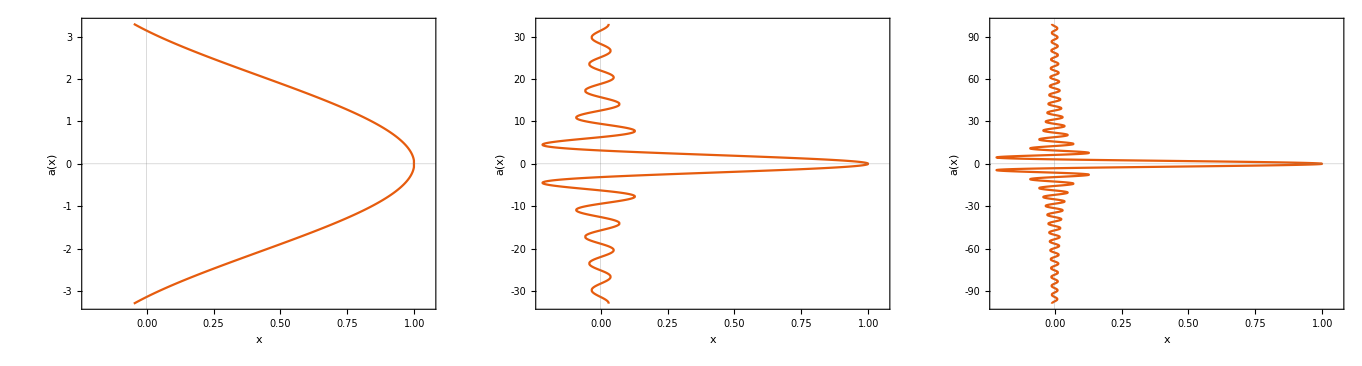

```mathematica
GraphicsRow[
{finalPlot[3,1000],
finalPlot[30,1000],
finalPlot[90,1000]},Spacings->0]
```

```mathematica
Export[
NotebookDirectory[]<>"plot.png",
GraphicsRow[
{finalPlot[3,1000],
finalPlot[30,1000],
finalPlot[90,1000]},Spacings->0]];
```